# Module 4: Probability models

## Slide Show Subtitle

## 1. Stochastic and deterministic models

## 2. Rental cars

The probability of car rented at place A, being in place A after n rentals can be described by a recursion. For each step step n, the probability for the car ending in A is the probability for the car starting in A and ending in A, plus the probability for the car starting in B and ending in A.

```mathematica
Pa[0]:=1
Pa[n_]:=Pa[n-1]*0.6+(1-Pa[n-1])*0.3
```

The probability can be converted to an equation of the following form:

```mathematica
PaEqn[n]:=1-Sum[0.4*0.3^m,{m,0,n-1}]
```

Should one wish to calculate the probability for a car starting at place B ending in A, one could use the same recursion as above, but replace the initial probability with zero. This since the probability of a car starting in B being in place A after zero rentals is zero, except for quantum cars which may be at both places at any moment.

### 2b. Long run proportions

To find out how many cars are in A and B in the long run we can see that when we use the formula from 2a after a while we always end up with the same procentage of cars cars in A or rather the decrease is not significant after n>14 where the probability of a car rented in A finds itself in A againis 42.8571%. Over time every car in B should have been in A once and therefore the cars in B are irrelivant when calculating how many cars will end up in A. Likewise a fomrula similar to the one in 2a adjusted with the probabilities for B gives us the answer that over time 57.1429% of cars starting in B will return to B. So in total we get 57.1429% of all cars in B and 42.8571% of all cars in A.

### 2c. Expected proportion of cars, given starting values

Apart from knowing the expected number of cars after a given number of iterations, one might want to extend the number in a number of ways to make it more usable, for example by taking the following into account:

Support different rental periods or rental intensities at different stations, the current model assumes that car rentals happens in synchronized steps at both stations.

Support more than two stations, in a real-world setting we would have to handle multiple stations, for each station pair (A,B) we would need a probability for a car picked up at A to be returned at B.

Answer questions such as: After three months, what is the probability that there will be less than five cars at any station?

## 3. Analyzing a Markov chain

We fed the program with a rather long (~15kb) text in english about the challenges of ensuring fresh water to a growing world population. For gradually increasing values of k, we got text that was more and more readable, see snippets in table below.

k=0 | "iti ipd dlearntsste ir oeedffih"
k=1 | "oupre torepand tit r bes analan"
k=2 | "Liquid of agen is nough scall ties"
k=3 | "thereby some farmers descussity"
k=4 | "as the rain due come more is the"
k=5 | "sent desaline aquifires of Mexico"

One of us once wrote a chat robot which used a large amount of newspaper articles to create readable sentences of gibberish. Put in a public chat room, it used the words written by others as a starting point and searched for words that where likely to follow.
The value of k controls how many characters of the recent output sequence that should be used to figure out the next character. With k=0 we would expect a random output sequence, since no charatcers is used. By setting k=1 we get a set of pronouncable words, this because a wovel is usually followed by a consonant and vice versa in ordinary english, likewise the output has similar properties. Gradually the sequences becomes better and better when more data is used for character prediction.

How can the algorithm escape a throng of dogs?

Given that only the last k characters in the output string is used for prediction, we figured that it should be possible to trap the algorithm in a repeating sequence. If we set k=4 and add a large amount of repeating three-letter words separated by a space, for example “dog dog dog...” to the document, once the algortihm stumbles upon the word “dog “, it should instantly get trapped. The most likely character to follow “ dog” would be “ “, to follow “dog “ would be “d”, to follow “og d” would be o and so on. The trick seems to work, after a rant of gibberish, the algorithm is trapped:
“...which water timest is nearth-eashink of thesensive at than dog dog dog dog dog...”.
However, after a while, it escapes: “...dog dog dog dog dog dog desire the not set one commodity...”.

How can this happen? Is the compactly written C program doing something fishy, not covered in the assignment description?

## 4. Risk of infection

Given the problem description there are essentially four different scenarious, each with their own probability distribution.

Diagnosed | Actual state | Equation | Probability
Healthy | Healthy | 99.7%*97% | 96.709%
Healthy | Sick | 0.3%*1% | 0.003%
Sick | Healthy | 99.7%*3% | 2.991%
Sick | Sick | 0.3%*99% | 0.297%

To get the probability for someone being diagnosed as sick to actually be sick, we simply divide the probability of correctly being diagnosed sick with the total probability of being diagnosed sick.
P(Sick | Diagnosed sick) =(0.297%)/(0.297%+2.991%)≈9%

## 5. Bayesian networks

### 5a. Trying out the Bayesian network

Probabilities change when we make observations. Bronchitis for example changes from (T:0.45,F:0.55) to (T:0.51,F:0.49) when we make the observation that X-Ray is true. So the probability of bronchitis is higher, since when the X-Ray was true then the probability of having Either tub. or lung cancer increases and in turn Lung cancer as well which means that the probability of smoking is heigher which heightens the probability of bronchitis.

### 5b. The joint probability distribution

The join probability distribution described mathematiclly with each probability variable and what it depends on : p(x1..xn|variables x depends on).
p(x1,x2,x3,x4,x5,x6,x7,x8)=p(x1)p(x2)*p(x3|x1)p(x4|x1)p(x5|x2)*p(x6|x4,x5)*p(x7|x3,x6)p(x8|x6)

### 5c. Explaining how the calculation in problem 4 can be described using a bayesian network

P(x1,x2)=p(x1)*p(x1|x2) where x1 is a sick person and x1’ is a healthy person, x2 is diagnosed sick and x2’ is diagnosed healthy.
Posterior | Renormalize | Prior | Likelihood function | Values
p(x1,x2|x2=1) | Prior*Likelihood | p(x1,x2) | *p(x2=1|x1,x2) | x1,x2
0 | 0 | 96.709 | 0 | 0,0
0.91% | 2.991% | 2.991% | 1 | 0,1
0 | 0 | 0.003% | 0 | 1,0
0.09% | 0.297% | 0.297% | 1 | 1,1

### 5d. Updating possibilities

To update our probability table we simply enter whichever obervation we make and let the equation calculate the answer for us similarly to how we did it in 5c. For example it would look like this if X-ray=true: p(x1,x2,x3,x4,x5,x6,x7,x8|x8=1)=p(x1)p(x2)*p(x3|x1)p(x4|x1)p(x5|x2)*p(x6|x4,x5)*p(x7|x3,x6)p(x8|x6) *p(x8=1|x1,x2,x3,x4,x5,x6,x7,x8)

After which we would devide each probability with (x1+x2+x3+x4+x5+x6+x7) in order to renormalize it.

### 5e. The Hugin system

## 6. Will it rain tomorrow?

To simplify the problem a bit, we assume that each day of the year has a specific probability of precipation, and that there are no trends between years. The task of predicting the probability of rain on a specific day, is thus the same as estimating the average rain frequency over an infinite period, using only a small sample.
The assignments suggests three strategies for estimating the average, each strategy has span of days which are to be averaged to arrive at an estiamte. Intuitively, this seem like the wrong way to go about. Instead we suggest using the all data available, but weight how the days contributes by using a bell curve. A nearly flat curve would be used when only short series of data is available, thus weighting all days equally. When longer data series are available, the bell curve can be allowed a higher top and a more spike like form, giving higher weight to days close to the examined, and less weight to other days of the year.

#### Large data set

Plot[#[NormalDistribution[0,0.3],x]/.{pdfx→PDF},{x,-5,5},AxesLabel→TraditionalForm/@{x,#[x]},Ticks→None,PlotRange→All,PlotStyle→Red]&/@{pdfx}

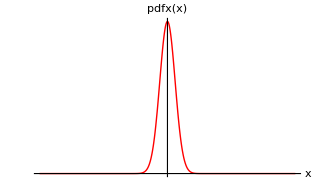

#### Small data set

Plot[#[NormalDistribution[0,3],x]/.{pdfx→PDF},{x,-5,5},AxesLabel→TraditionalForm/@{x,#[x]},Ticks→None,PlotRange→All,PlotStyle→Red]&/@{pdfx}

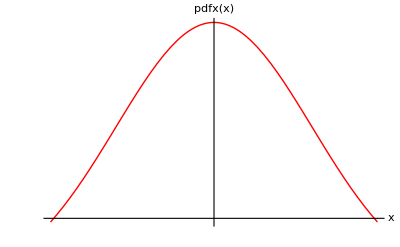

## 7. Reflection on previous module

### 7a. Attendance

We were both at the follow-up lecture and it looked like we had the right idea about all of the problems.

### 7b. Discussions with other groups

### 7c. Reflection over module 3